## Optimal Execution with Limit and Market Orders

## 8.2 Liquidation with Only Limit Orders

```mathematica
ω[t_,q_]:= ∑_(n=0)^q tλ^n/(n!)*ⅇ^(-κ*α*(q-n)^2)*(T-t)^n
ω[t_,q_]:=ⅇ^(-κ*α*q^2)/;t==T
ω[t_,q_]:=1/;q== 0
```

```mathematica
δ[t_,q_]:=1/κ*(1+Log[ω[t,q]/ω[t,q-1]])
```

```mathematica
λ=50/60;
tλ=λ*ⅇ^-1;

κ=100.0;
T=60;
α=10^-3;
𝒩=5;
σ=0.01;
```

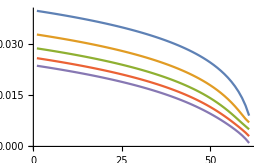

```mathematica
ListLinePlot@Table[Table[N@δ[t,q],{t,0,T}],{q,1,5}](*α-> 10^-3*)
```

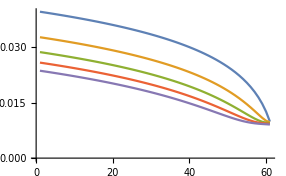

```mathematica
ListLinePlot@Table[Table[N@δ[t,q],{t,0,T}],{q,1,5}](*α-> 10^-4*)
```

#### Numerical Experiments

```mathematica
(*Price Dynamics*)
S0=30;
𝒫=TransformedProcess[S0+σ*(W[t]),{W\[Distributed]WienerProcess[]},t];
```

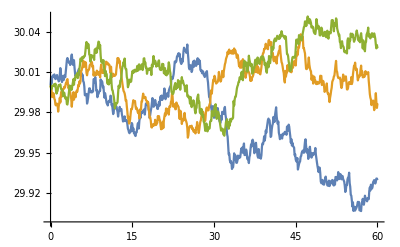

```mathematica
With[{data = RandomFunction[𝒫,{0,T,0.1},3]},
ListLinePlot[data,PlotRange->All]]
```

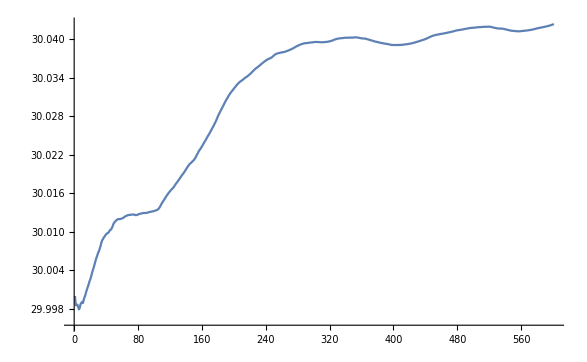

```mathematica
ListLinePlot@With[{d=Transpose[Normal[RandomFunction[𝒫,{0,T,0.1},1]][[1]]][[2]]},Table[Mean[d[[;;i]]],{i,1,Length@d}]]
```

```mathematica
dt= RandomFunction[𝒫,{0,T,0.1},1]
```

TemporalData[…]

```mathematica
dt[[2]][[1]][[1]][[2;;]]
```

{29.9972}

```mathematica
Range[0,60,0.1][[2;;]]
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.,20.1,20.2,20.3,20.4,20.5,20.6,20.7,20.8,20.9,21.,21.1,21.2,21.3,21.4,21.5,21.6,21.7,21.8,21.9,22.,22.1,22.2,22.3,22.4,22.5,22.6,22.7,22.8,22.9,23.,23.1,23.2,23.3,23.4,23.5,23.6,23.7,23.8,23.9,24.,24.1,24.2,24.3,24.4,24.5,24.6,24.7,24.8,24.9,25.,25.1,25.2,25.3,25.4,25.5,25.6,25.7,25.8,25.9,26.,26.1,26.2,26.3,26.4,26.5,26.6,26.7,26.8,26.9,27.,27.1,27.2,27.3,27.4,27.5,27.6,27.7,27.8,27.9,28.,28.1,28.2,28.3,28.4,28.5,28.6,28.7,28.8,28.9,29.,29.1,29.2,29.3,29.4,29.5,29.6,29.7,29.8,29.9,30.,30.1,30.2,30.3,30.4,30.5,30.6,30.7,30.8,30.9,31.,31.1,31.2,31.3,31.4,31.5,31.6,31.7,31.8,31.9,32.,32.1,32.2,32.3,32.4,32.5,32.6,32.7,32.8,32.9,33.,33.1,33.2,33.3,33.4,33.5,33.6,33.7,33.8,33.9,34.,34.1,34.2,34.3,34.4,34.5,34.6,34.7,34.8,34.9,35.,35.1,35.2,35.3,35.4,35.5,35.6,35.7,35.8,35.9,36.,36.1,36.2,36.3,36.4,36.5,36.6,36.7,36.8,36.9,37.,37.1,37.2,37.3,37.4,37.5,37.6,37.7,37.8,37.9,38.,38.1,38.2,38.3,38.4,38.5,38.6,38.7,38.8,38.9,39.,39.1,39.2,39.3,39.4,39.5,39.6,39.7,39.8,39.9,40.,40.1,40.2,40.3,40.4,40.5,40.6,40.7,40.8,40.9,41.,41.1,41.2,41.3,41.4,41.5,41.6,41.7,41.8,41.9,42.,42.1,42.2,42.3,42.4,42.5,42.6,42.7,42.8,42.9,43.,43.1,43.2,43.3,43.4,43.5,43.6,43.7,43.8,43.9,44.,44.1,44.2,44.3,44.4,44.5,44.6,44.7,44.8,44.9,45.,45.1,45.2,45.3,45.4,45.5,45.6,45.7,45.8,45.9,46.,46.1,46.2,46.3,46.4,46.5,46.6,46.7,46.8,46.9,47.,47.1,47.2,47.3,47.4,47.5,47.6,47.7,47.8,47.9,48.,48.1,48.2,48.3,48.4,48.5,48.6,48.7,48.8,48.9,49.,49.1,49.2,49.3,49.4,49.5,49.6,49.7,49.8,49.9,50.,50.1,50.2,50.3,50.4,50.5,50.6,50.7,50.8,50.9,51.,51.1,51.2,51.3,51.4,51.5,51.6,51.7,51.8,51.9,52.,52.1,52.2,52.3,52.4,52.5,52.6,52.7,52.8,52.9,53.,53.1,53.2,53.3,53.4,53.5,53.6,53.7,53.8,53.9,54.,54.1,54.2,54.3,54.4,54.5,54.6,54.7,54.8,54.9,55.,55.1,55.2,55.3,55.4,55.5,55.6,55.7,55.8,55.9,56.,56.1,56.2,56.3,56.4,56.5,56.6,56.7,56.8,56.9,57.,57.1,57.2,57.3,57.4,57.5,57.6,57.7,57.8,57.9,58.,58.1,58.2,58.3,58.4,58.5,58.6,58.7,58.8,58.9,59.,59.1,59.2,59.3,59.4,59.5,59.6,59.7,59.8,59.9,60.}

```mathematica
dt[[;;1]]
```

TemporalData::ntprs: The argument Automatic at position 1 is expected to be a list of time-value pairs or a list of states with equal dimensionality.

TemporalData[Automatic]

```mathematica
backTest[_,_]:=
```